Άσκηση O1

Θεωρούμε τον ταλαντωτή

x^(..)=-1-x^3+a x^2+e cost, 0<a≤3, 0<e<0.5

Σχεδιάστε την τομή Poincare του συστήματος για μια δικής σας επιλογή των σταθερών a και e. Επιλέξτε κατάλληλα τις σταθερές ώστε να έχετε παρουσία κάποιων χαοτικών τροχιών.

Θέτουμε α=1.5, ε=0.19, και σχεδιάζουμε την τομή Poincare για χρόνο t_max=25000.
Τα σημεία με κόκκινο δείχνουν τις αρχικές συνθήκες.

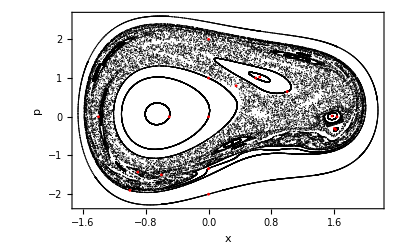

```mathematica
ClearAll["Global`*"]
deq1=x'[t]==y[t];
deq2=y'[t]==-1-x[t]^3+a x[t]^2+e Sin[t];
a=1.5;
e=0.19;
tmax=25000;
initial={{0,1},{0,0},{0,2},{0,-2},{-0.5,0},{-1.4,0},{1.57,0.02},{1.633,0},{0.6,1},{1,0.65},{1.6,-0.3},{1.616,-0.3283},{-0.6,-1.5},{-1,-1.9},{-0.9,-1.43},{0.65,1.025},{0.35,0.8},{0,-1.34}};
pts=Flatten[First@Last@Reap@For[i=1,i≤Length[initial],i++,
sol=NDSolve[{deq1,deq2,x[0]==initial[[i,1]],y[0]==initial[[i,2]]},{x,y},{t,0,tmax}];
xt=-x/.sol[[1]];
yt=y/.sol[[1]];
Sow@Table[{xt[t],yt[t]},{t,0,tmax,2π}];
],1];
poincarePlot=ListPlot[pts,
Frame->True,
FrameLabel->{"x","p"},
PlotStyle->{Black,PointSize[0.002]},
ImageSize->Full,
PlotRange->All,
Epilog->{Red,PointSize[0.005],Point[initial]}
]
```

Επιλέξτε αρχικές συνθήκες για μια περιοδική, μια ημιπεριοδική, και μια χαοτική τροχιά.

Σχεδιάστε τη χρονική εξέλιξη x(t) για τις παραπάνω τροχιές.

Υπολογίστε και σχεδιάστε το φάσμα ισχύος για τις παραπάνω τροχιές.

Υπολογίστε και σχεδιάστε τον δείκτη FLI για τις παραπάνω τροχιές.

Επιλέγουμε τις τροχιές με αρχικές συνθήκες:

περιοδική:

Δεν μπόρεσα να εντοπίσω περιοδική τροχιά.

ημιπεριοδική: (0.306 , -0.6683)

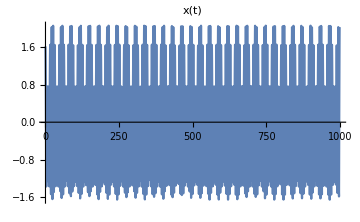
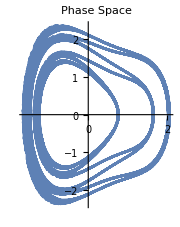
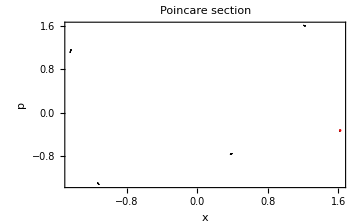
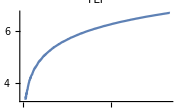
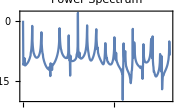

```mathematica
ClearAll["Global`*"]
x0=1.62;
y0=-0.3251;
deq1=x'[t]==y[t];
deq2=y'[t]==-1-x[t]^3+a x[t]^2+e Sin[t];
deq3=z1'[t]==z2[t];
deq4=z2'[t]==-e Sin[t]+a x[t]x'[t]-3 x[t]^2 x'[t];
a=1.5;
e=0.19;
tmax=1000;
sol=NDSolve[{deq1,deq2,deq3,deq4,x[0]==x0,y[0]==y0,z1[0]==1,z2[0]==0},{x,y,z1,z2},{t,0,tmax}];
xt=x/.sol[[1]];
yt=y/.sol[[1]];
z1t=z1/.sol[[1]];
z2t=z2/.sol[[1]];
(* διάγραμμα χώρου φάσεων και x(t) *)
plotX=Plot[xt[t],{t,0,tmax},PlotRange->{{0,tmax},All},ImageSize->Medium,PlotLabel->"x(t)"];
plotPhase=ParametricPlot[{xt[t],yt[t]},{t,0,tmax},ImageSize->Small,PlotLabel->"Phase Space"];
(* poincare *)
data=Table[{xt[t],yt[t]},{t,0,tmax,2π}];
plotPoincare=ListPlot[data,
Frame->True,
FrameLabel->{"x","p"},
PlotStyle->{Black,PointSize[0.002]},
ImageSize->Medium,
PlotRange->All,
Epilog->{Red,PointSize[0.005],Point[{x0,y0}]},
PlotLabel->"Poincare section"
];
(* FLI *)
FLI[t_]:=Log[10,z1t[t]^2+z2t[t]^2];
plotFLI=Plot[FLI[t],{t,0,tmax},PlotLabel->"FLI",ImageSize->Small];
(* φάσμα ισχύος *)
ndata=2^10;
dt=tmax/ndata;
sample=ParallelTable[xt[i dt],{i,0,ndata-1}];
fdata=Chop[Fourier[sample]];
powerSpectrum=ParallelTable[{i 2Pi/tmax,Log[(Re[fdata[[i]]]^2+Im[fdata[[i]]]^2)/(2 √ndata)]},{i,1,ndata/2}];plotPowerSpectrum=ListPlot[powerSpectrum,
Joined->True,
PlotRange->All,
Frame->True,
ImageSize->Small,
PlotLabel->"Power Spectrum"
];
(* παρουσίαση *)
Column[{
Row[{plotX,plotPhase}],
Row[{plotPoincare}],
Row[{plotFLI,plotPowerSpectrum}]
},Alignment->Center]
```

χαοτική: (1,0)

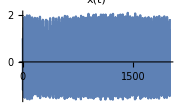
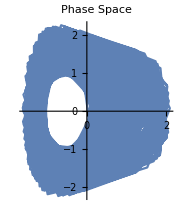
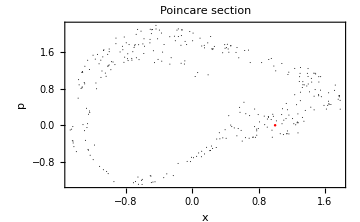
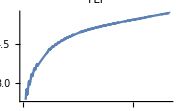
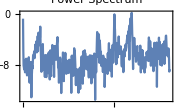

```mathematica
ClearAll["Global`*"]
x0=1;
y0=0;
deq1=x'[t]==y[t];
deq2=y'[t]==-1-x[t]^3+a x[t]^2+e Sin[t];
deq3=z1'[t]==z2[t];
deq4=z2'[t]==-e Sin[t]+a x[t]x'[t]-3 x[t]^2 x'[t];
a=1.5;
e=0.19;
tmax=2000;
sol=NDSolve[{deq1,deq2,deq3,deq4,x[0]==x0,y[0]==y0,z1[0]==1,z2[0]==0},{x,y,z1,z2},{t,0,tmax}];
xt=x/.sol[[1]];
yt=y/.sol[[1]];
z1t=z1/.sol[[1]];
z2t=z2/.sol[[1]];
(* διάγραμμα χώρου φάσεων και x(t) *)
plotX=Plot[xt[t],{t,0,tmax},PlotRange->{{0,tmax},All},ImageSize->Small,PlotLabel->"x(t)"];
plotPhase=ParametricPlot[{xt[t],yt[t]},{t,0,tmax},ImageSize->Small,PlotLabel->"Phase Space"];
(* poincare *)
data=Table[{xt[t],yt[t]},{t,0,tmax,2π}];
plotPoincare=ListPlot[data,
Frame->True,
FrameLabel->{"x","p"},
PlotStyle->{Black,PointSize[0.002]},
ImageSize->Medium,
PlotRange->All,
Epilog->{Red,PointSize[0.005],Point[{x0,y0}]},
PlotLabel->"Poincare section"
];
(* FLI *)
FLI[t_]:=Log[10,z1t[t]^2+z2t[t]^2];
plotFLI=Plot[FLI[t],{t,0,tmax},
PlotLabel->"FLI",
ImageSize->Small
];
(* φάσμα ισχύος *)
ndata=2^10;
dt=tmax/ndata;
sample=ParallelTable[xt[i dt],{i,0,ndata-1}];
fdata=Chop[Fourier[sample]];
powerSpectrum=ParallelTable[{i 2Pi/tmax,Log[(Re[fdata[[i]]]^2+Im[fdata[[i]]]^2)/(2 √ndata)]},{i,1,ndata/2}];plotPowerSpectrum=ListPlot[powerSpectrum,
Joined->True,
PlotRange->All,
Frame->True,
ImageSize->Small,
PlotLabel->"Power Spectrum"
];
(* παρουσίαση *)
Column[{
Row[{plotX,plotPhase}],
Row[{plotPoincare}],
Row[{plotFLI,plotPowerSpectrum}]
},Alignment->Center]
```

Η τροχιά αυτή δείχνει χαοτική, αλλά ο ρυθμός αύξησης του δείκτη FLI δείχνει να μειώνεται με τον χρόνο, που δεν θα ‘πρεπε να συμβαίνει για μια χαοτική τροχιά.